# Quantum states of systems of chemical interest using NDEigensystem

Single sentence description of the topic

## Hamiltonian operator for the Coulomb potential

Potential energy operator

```mathematica
𝒱[x__]:=-1/Norm[{x}]
```

Kinetic energy operator:

```mathematica
𝒦[ψ_][x__]:=-1/2∇_{x}^2 ψ[x]
```

Hamiltonian operator:

```mathematica
ℋ[ψ_][x__]:=𝒦[ψ][x]+𝒱[x]ψ[x]
```

#### Exercises:

Obtain the Hamiltonian for the Hydrogen atom in 1, 2, and 3 dimensions

Write the Schrodinger equation for the 1 dimensional Hydrogen atom.

## 1-Dimensional Hydrogen atom

### Analytical solutions for the 1 dimensional Hydrogen atom

Schrodinger equation for the 1 dimensional Hydrogen atom can be written as Kummer’s equation. The solutions of Kummer’s equation are the confluent hypergeometric functions Hypergeometric1F1[1-n,2, 2 x/n] .

Analytical solutions:

```mathematica
Subscript[f, n_][x_]:=x Exp[-x/n]Hypergeometric1F1[1-n,2, 2 x/n]
```

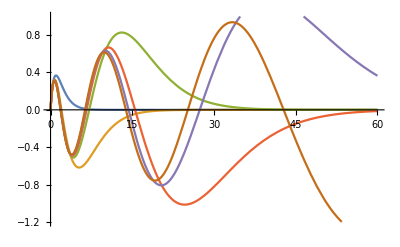

```mathematica
Plot[Evaluate@Table[Subscript[f, i][x],{i,1,6}],{x,0,60},PlotRange->{-1.2,1}]
```

In atomic units,the energies of the four lowest eigenstates are:

```mathematica
Subscript[ℰ, 1]=Table[N[-1/(2 i^2)],{i,1,6}]
```

{-0.5,-0.125,-0.0555556,-0.03125,-0.02,-0.0138889}

#### Exercises:

Are these functions normalized? If not, find the normalization constants for each eigenstate.

Define a normalized function.

#### Answer:

Find the normalization constant for each state:

```mathematica
nint=Table[NIntegrate[(Subscript[f, n][x])^2,{x,0,100}],{n,1,6}]
```

{0.25,2.,6.75,16.,31.25,53.9357}

The normalization constant is

```mathematica
norm=1/Sqrt[nint]
```

{2.,0.707107,0.3849,0.25,0.178886,0.136164}

Normalization:

```mathematica
Subscript[Ψ, n_][x_]:=norm⟦n⟧ Subscript[f, n][x]
```

```mathematica
Table[NIntegrate[  Subscript[Ψ, i][x]^2,{x,0,100}],{i,1,6}]
```

{1.,1.,1.,1.,1.,1.}

### Boundary conditions

Physically the probability of finding the electron at x=0 should be zero. Computationally, the wave function should be zero at the end of the computational box. These requirements can be fulfilled using Dirichlet Boundary conditions.

Boundary conditions:

```mathematica
Subscript[ℬ, 1]=DirichletCondition[ψ[x]==0,True];
```

In atomic units, the energies of the four lowest eigenstates are:

### Eigensystem

For a box of length l, the n lowest energy eigenstates are obtained with the function eigensystem[n,l]:

```mathematica
eigensystem[ne_,ℓ_]:=
SortBy[
Transpose[
NDEigensystem[{ℋ[ψ][x],Subscript[ℬ, 1]},ψ,
{x,0,ℓ},ne,Method-> {"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}]],
First]
```

The eigenvalue (en) and the wave function can be obtained by using:

```mathematica
{en,wf}=eigensystem[50,10]⟦1⟧
```

{-0.499998,InterpolatingFunction[{{0., 10.}}, <>]}

For example, for the ground state:

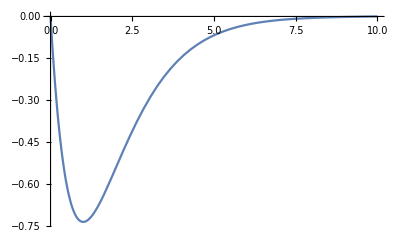

```mathematica
Plot[wf[x],{x,0,10}]
```

#### Exercise:

Verify that the eigenstates of eigensystem[n,l] are normalized.

Plot the ground state, and the first excited state. What are their energies?

#### Solution:

For example, for the 5th eigenstate obtained from a calculation of 10 states and a box of length 10 atomic units:

```mathematica
NIntegrate[(eigensystem[10,10]⟦5,2⟧[x])^2,{x,0,10}]
```

1.

```mathematica
wf1=eigensystem[10,10][[1,2]];
wf2=eigensystem[10,10][[2,2]];
```

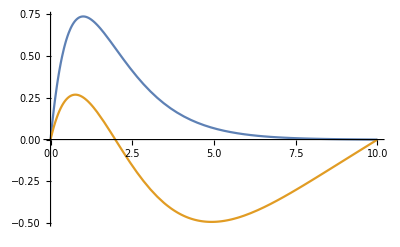

```mathematica
Plot[{wf1[x],wf2[x]},{x,0,10}]
```

### Results for the 4 lowest energy eigenstates

Quality of the eigenvalues and eigenvectors:

```mathematica
Manipulate[
GraphicsGrid@
Partition[
(es↦Table[
Show[
Plot[{es⟦i,1⟧+(es⟦i,2⟧[x])^2,𝒱[x],Subscript[ℰ, 1]⟦i⟧+(Subscript[Ψ, i][x]^2)},{x,0,40},
PlotRange->{-0.6,0.1},
Filling->{1->es⟦i,1⟧,2-> Bottom,None}(*,
PlotLabel->label[i,es⟦i,1⟧,Subscript[ℰ, 1]⟦i⟧]*)]
],
{i,1,4}
])@
eigensystem[ne,ℓ],
2],
{{ℓ,15,"Box Length"},5,40,5},
{{ne,5,"Number of eigenfunctions"},10,40,5}
]
```

#### Investigations

Use the sliding menus of the Manipulate to explore the solutions of NDEigensystem. Answer the following questions :

Determine the range in the parameters n and l for obtaining good agreement with the analytical results?

What should be the frequency of a photon to detach an electron in the 1D hydrogen atom?

What is the frequency of the emitted photon when the electron undergoes a transition between the first excited and the ground states?

## 2-Dimensional Hydrogen atom

### Analytical solutions

#### The radial function:

The analytical radial functions are given by R[n,l,r]

```mathematica
β[n_]=2/(n-1/2);
Ν[n_,l_]:=(((n+Abs[l]-1)!)/((2 n-1)(n-Abs[l]-1)!))^(1/2);
R[n_,l_,r_]:=β[n]Ν[n,l](β[n] r)^Abs[l] Exp[-β[n] r/2]HypergeometricU[-n+Abs[l]+1,2 Abs[l]+1,β[n] r];
```

Radial wave functions for l=0:

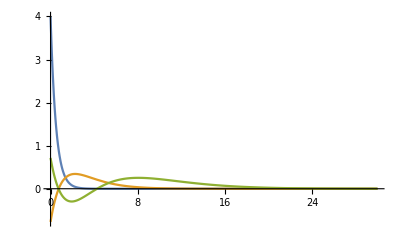

```mathematica
plotRa=Plot[Evaluate@Table[R[i,0,x],{i,1,3}],{x,0,30},PlotRange->All]
```

Radial wave functions for l=1:

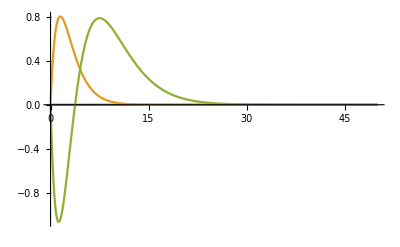

```mathematica
plotRa=Plot[Evaluate@Table[R[i,1,x],{i,1,3}],{x,0,50},PlotRange->All]
```

In atomic units, the energies of the four lowest eigenstates are:

```mathematica
Subscript[ℰ, 2]=Table[-N[1/(2(n-1/2)^2)],{n,1,10}]
```

{-2.,-0.222222,-0.08,-0.0408163,-0.0246914,-0.0165289,-0.0118343,-0.00888889,-0.00692042,-0.00554017}

#### Exercise

Are these functions normalized?

The wave function depends now on two quantum numbers. What is the meaning of them?

#### Answer

Normalizarion

```mathematica
Column[Table[NIntegrate[R[i,j,r]^2, {r,0,200}],{i,1,4},{j,-i+1,i-1}] ]
```

{4.}
{1.77778,0.444444,1.77778}
{92.16,5.76,0.64,5.76,92.16}
{42318.4,1175.51,47.0204,2.93878,47.0204,1175.51,42318.4}

#### The angular function:

As we saw before, the angular part has the eigenfunctions:

```mathematica
Φ[l_,ϕ_]:=1/(√(2π))Exp[I l ϕ]
```

Plotting the angular functions Φ[l,ϕ]:

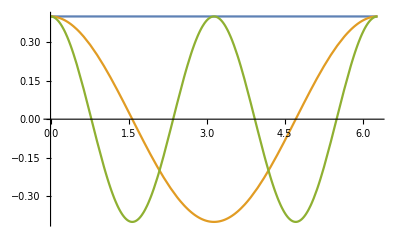

```mathematica
Plot[{Re[Φ[0,ϕ]],Re[Φ[1,ϕ]],Re[Φ[2,ϕ]]},{ϕ,0,2Pi}]
```

#### Exercise

Plot a graphics of the full wave function

Are these functions normalized?

#### Answer

The transformation from polar to Cartesian coordinates:

```mathematica
tocc=Thread[{r,ϕ}->ToPolarCoordinates[{x,y}]]
```

{r→√(x^2+y^2),ϕ→ArcTan[x,y]}

```mathematica
Plot3D[Re[R[1,0,r]Φ[0,ϕ]]/.tocc,{x,-5,5},{y,-5,5},PlotRange->All]
```

-Graphics3D-

```mathematica
NIntegrate[Abs[R[1,0,r]Φ[0,ϕ]]^2/.tocc,{x,-10,10},{y,-10,10}]
```

1.

```mathematica
ContourPlot[Re[R[2,0,r]Φ[0,ϕ]]/.tocc,{x,-10,10},{y,-10,10},PlotRange->All,PlotPoints->25,]
```

ContourPlot::nonopt: Options expected (instead of Null) beyond position 3 in ContourPlot[Re[R[2,0,r] Φ[0,ϕ]]/.tocc,{x,-10,10},{y,-10,10},PlotRange→All,PlotPoints→25,Null]. An option must be a rule or a list of rules.

ContourPlot[Re[R[2,0,r] Φ[0,ϕ]]/.tocc,{x,-10,10},{y,-10,10},PlotRange→All,PlotPoints→25,Null]

```mathematica
NIntegrate[Abs[R[2,0,r]Φ[0,ϕ]]^2/.tocc,{x,-10,10},{y,-10,10}]
```

0.999351

```mathematica
NIntegrate[r Abs[R[2,0,r]Φ[0,ϕ]]^2,{r,0,10},{ϕ,0,2 π}]
```

0.998601

```mathematica
Plot3D[Im[R[2,1,r]Φ[1,ϕ]]/.tocc,{x,-10,10},{y,-10,10},PlotRange->All]
```

-Graphics3D-

```mathematica
NIntegrate[r Abs[R[2,1,r]Φ[1,ϕ]]^2,{r,0,10},{ϕ,0,2 π}]
```

3.99677

```mathematica
NIntegrate[Abs[R[2,1,r]Φ[1,ϕ]]^2/.tocc,{x,-20,20},{y,-20,20}]
```

4.

### Boundary conditions and integration region

The analytical solutions showed that there are two types of states:
- even states which are not zero at the origin
- odd states which are zero at the origin

The Dirichlet Boundary condition for the even and odd states is given by:

```mathematica
Subscript[ℬ, 2]=DirichletCondition[ψ[x,y]==0,True]
```

DirichletCondition[ψ[x,y]==0,True]

With the integration region:

```mathematica
Subscript[𝒜, 2][Rin_,Rout_]:=Annulus[{0,0},{Rin,Rout}]
```

```mathematica
Subscript[𝒟, 2][R_]:=Disk[{0,0},R];
```

The integration region looks like:

-Graphics-



```mathematica
Graphics[Subscript[𝒜, 2][0.1,1]]
Graphics[Subscript[𝒟, 2][1]]
```

#### Exercise:

Why the integration region has this form?

### Eigensystem Annulus

```mathematica
(*Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.5}}}}*)
(*Method->{"Eigensystem"->{"Arnoldi","MaxIterations"->10000}}*)
```

```mathematica
eigensystem1[ne_,Rin_,Rout_]:=
SortBy[
Transpose[NDEigensystem[{ℋ[ψ][x,y],Subscript[ℬ, 2]},ψ[x,y],{x,y}∈Subscript[𝒜, 2][Rin,Rout],ne,Method->{"Eigensystem"->{"Arnoldi","MaxIterations"->10000}}]],First]
```

```mathematica
eigensys1=eigensystem1[20,0.1,20];
```

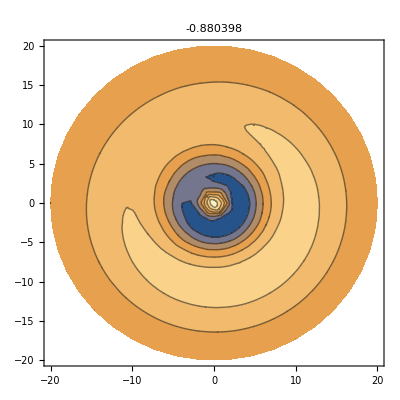
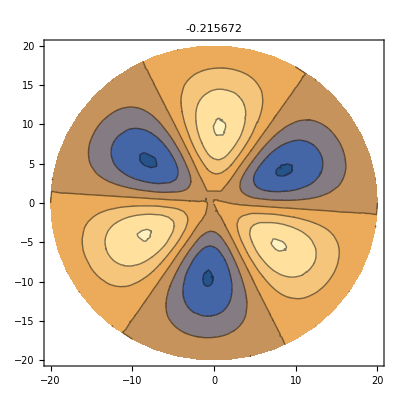
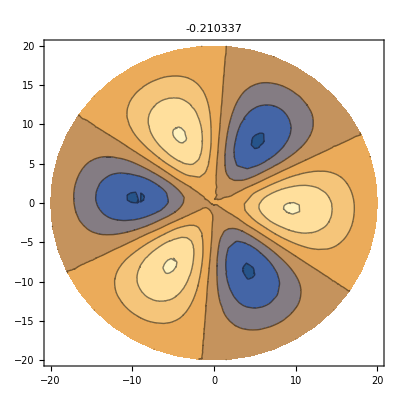
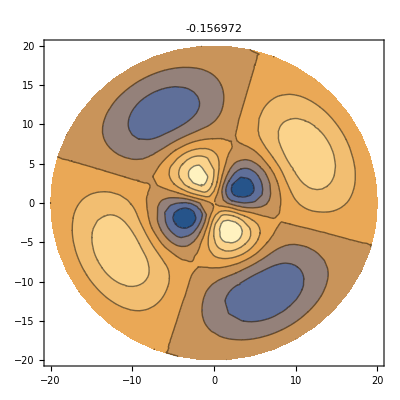

```mathematica
Table[ContourPlot[eigensys1[[i,2]],Evaluate[{x,y}∈Subscript[𝒜, 2][0.1,20]],PlotRange->All,PlotPoints->25,PlotLabel->eigensys2⟦i,1⟧],{i,1,4}]
```

### Eigensystem Disk

```mathematica
eigensystem2[ne_,R_]:=
SortBy[
Transpose[NDEigensystem[{ℋ[ψ][x,y],Subscript[ℬ, 2]},ψ[x,y],{x,y}∈Subscript[𝒟, 2][R],ne,Method->{"Eigensystem"->{"Arnoldi","MaxIterations"->10000}}]],First]
```

```mathematica
eigensys2=eigensystem2[20,20];
```

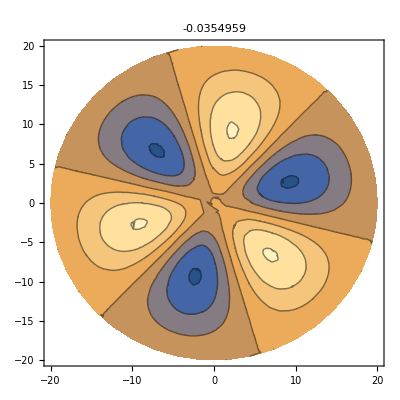
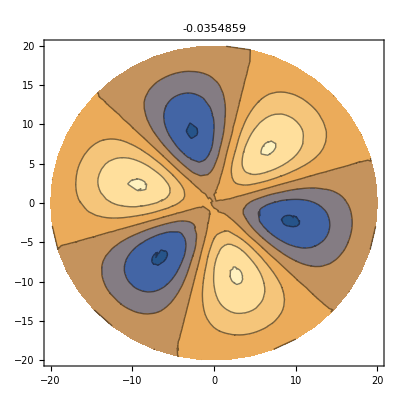
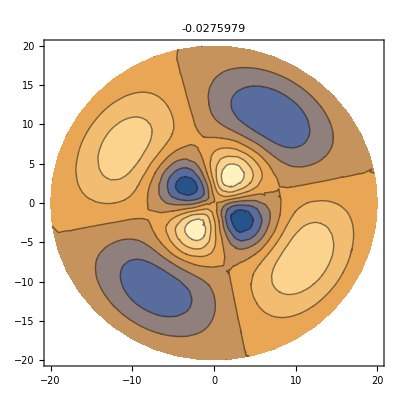
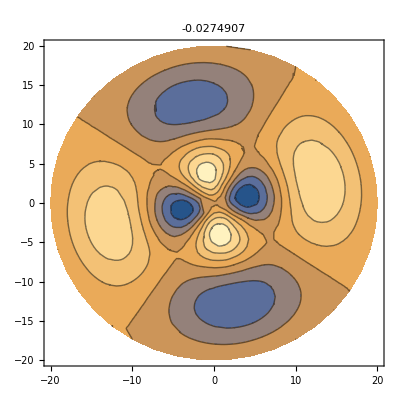

```mathematica
Table[ContourPlot[eigensys2[[i,2]],Evaluate[{x,y}∈Subscript[𝒟, 2][20]],PlotRange->All,PlotPoints->25,PlotLabel->eigensys2⟦i,1⟧],{i,1,4}]
```

```mathematica
Plot3D[temp[[2,1]],{x,y}∈Evaluate[Subscript[ℛ, 2]/.R->10.]]
```

Plot3D::idomdim: {x,y}∈Evaluate[ℛ_2/.R→10.] does not have a valid dimension as a plotting domain.

Plot3D[temp⟦2,1⟧,{x,y}∈Evaluate[ℛ_2/.R→10.]]

Calculation of the 4 lowest energy eigenstates of the Hydrogen atom for different choices  of the calculation box ℓ, and the size of the spatial discretization Δx.

```mathematica
Manipulate[
Table[Plot3D[#⟦i,2⟧,{x,y}∈Evaluate[Subscript[ℛ, 2]/.R->rmax],PlotRange->All,PlotLabel->StringTemplate["E_(``) = `` (``)"][i,#⟦i,1⟧,Subscript[ℰ, 1]⟦i⟧]],{i,1,4}]&@SortBy[Transpose[NDEigensystem[{Subscript[ℋ, 2][ψ[x,y]],Subscript[ℬ, 2]},ψ[x,y],{x,y}∈Subscript[ℛ, 2]/.R-> rmax,40,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->Δx}}}}]],First],"R"->{rmax,2,62,10},"Δx"-> {Δx,0.1,0.01,-0.01}]
```

```mathematica
Laplacian[
```

```mathematica
Plot3D[temp[[2,1]],{x,y}∈Evaluate[Subscript[ℛ, 2]/.R->10.]]
```

Plot3D::idomdim: {x,y}∈Evaluate[ℛ_2/.R→10.] does not have a valid dimension as a plotting domain.

Plot3D[temp⟦2,1⟧,{x,y}∈Evaluate[ℛ_2/.R→10.]]

Calculation of the 4 lowest energy eigenstates of the Hydrogen atom for different choices  of the calculation box ℓ, and the size of the spatial discretization Δx.

```mathematica
Manipulate[
Table[Plot3D[#⟦i,2⟧,{x,y}∈Evaluate[Subscript[ℛ, 2]/.R->rmax],PlotRange->All,PlotLabel->StringTemplate["E_(``) = `` (``)"][i,#⟦i,1⟧,Subscript[ℰ, 1]⟦i⟧]],{i,1,4}]&@SortBy[Transpose[NDEigensystem[{Subscript[ℋ, 2][ψ[x,y]],Subscript[ℬ, 2]},ψ[x,y],{x,y}∈Subscript[ℛ, 2]/.R-> rmax,40,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->Δx}}}}]],First],"R"->{rmax,2,62,10},"Δx"-> {Δx,0.1,0.01,-0.01}]
```

```mathematica
Laplacian[
```

Further Explorations

Name of a related topic for exploration

Name of another related topics for exploration (repeat as needed)

Authorship information

Name of Author

Date of creation

Author email address (please use the email associated with your Wolfram User ID)

PredictiveInterface`DoPredictionAction::newsess: Suggested actions are only available in the same kernel session that suggested them.